```mathematica
ClearAll[v1,v2,ν,ω,λ1,λ2,v1,v2]
A1={{0,ω},{-ω,-ν}};
A2 = {{0,ω},{ω,-ν}};
(*{{l2,l1},{v2,v1}}*)
{{λ2,λ1},{v2,v1}}= Eigensystem[A1];
λ1
MatrixForm[v1]
λ2
MatrixForm[v2]
ClearAll[v1,v2,ν,ω,λ1,λ2,v1,v2]
{{λ2,λ1},{v2,v1}}= Eigensystem[A2];
λ1
MatrixForm[v1]
λ2
MatrixForm[v2]
```

1/2 (-ν+√(ν^2-4 ω^2))

(-(ν+√(ν^2-4 ω^2))/(2 ω)
1)

1/2 (-ν-√(ν^2-4 ω^2))

(-(ν-√(ν^2-4 ω^2))/(2 ω)
1)

1/2 (-ν+√(ν^2+4 ω^2))

(-(-ν-√(ν^2+4 ω^2))/(2 ω)
1)

1/2 (-ν-√(ν^2+4 ω^2))

(-(-ν+√(ν^2+4 ω^2))/(2 ω)
1)

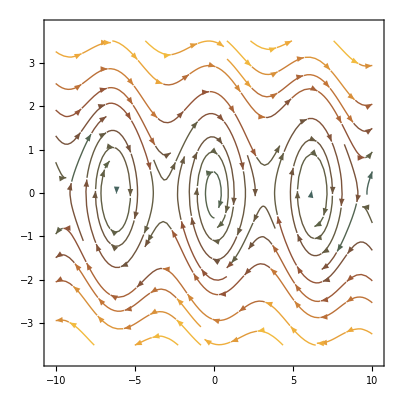

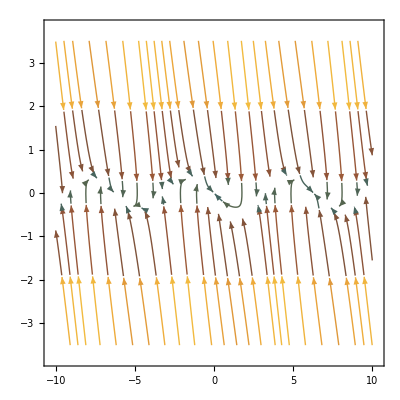

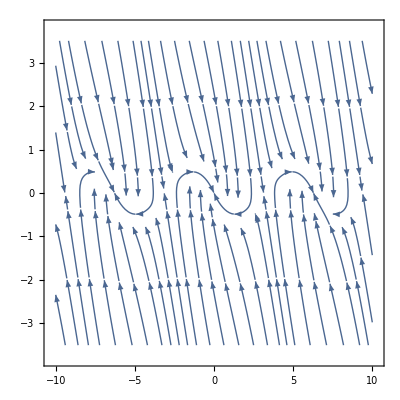

```mathematica
fx = ω y;
fy = -ν y - ω Sin[x];
StreamPlot[{fx/.{ν->.1,ω->1},fy/.{ν->.1,ω->1}},{x,-10,10},{y,-3.5,3.5},StreamColorFunction->"FallColors"]
StreamPlot[{fx/.{ν->5,ω->1},fy/.{ν->3,ω->1}},{x,-10,10},{y,-3.5,3.5},StreamColorFunction->"FallColors"]
StreamPlot[{fx/.{ν->2,ω->1},fy/.{ν->2,ω->1}},{x,-10,10},{y,-3.5,3.5}]
```

```mathematica
(* ----------------------------------------------------- *)
```

```mathematica
(*        {{λ2,λ1},{v2,v1}}        *)
```

```mathematica
AA={{-2,1},{1,-2}};
BB={{3,-2},{2,-2}};
CC={{1,1},{-5,-3}};
DD={{-1,5},{-2,5}};
EE={{3,2},{-2,-1}};
FF={{1,0},{5,-5}};
GG={{-2,0},{1,-3}};
HH={{-2,4},{1,1}};
II={{-1,1},{-1,-3}};
JJ={{1,1},{1,-3}};
KK={{0,-1},{2,-2}};
LL={{0,-1},{-2,-2}};
```

```mathematica
Eigensystem[AA]
Eigensystem[BB]
Eigensystem[CC]
Eigensystem[DD]
Eigensystem[EE]
Eigensystem[FF]
Eigensystem[GG]
Eigensystem[HH]
Eigensystem[II]
Eigensystem[JJ]
Eigensystem[KK]
Eigensystem[LL]
```

{{-3,-1},{{-1,1},{1,1}}}

{{2,-1},{{2,1},{1,2}}}

{{-1+ⅈ,-1-ⅈ},{{-2-ⅈ,5},{-2+ⅈ,5}}}

{{2+ⅈ,2-ⅈ},{{3-ⅈ,2},{3+ⅈ,2}}}

{{1,1},{{-1,1},{0,0}}}

{{-5,1},{{0,1},{6,5}}}

{{-3,-2},{{0,1},{1,1}}}

{{-3,2},{{-4,1},{1,1}}}

{{-2,-2},{{-1,1},{0,0}}}

{{-1-√5,-1+√5},{{2-√5,1},{2+√5,1}}}

{{-1+ⅈ,-1-ⅈ},{{1+ⅈ,2},{1-ⅈ,2}}}

{{-1-√3,-1+√3},{{1/2 (-1+√3),1},{1/2 (-1-√3),1}}}